# Higher genus nonorientable of genus04

Aug 03, 2020
Shin Kaneda

```mathematica
<<Own`Mesh`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Weierstrass data

```mathematica
Clear[k,h,r];
```

```mathematica
h=2;
k=2h;
```

```mathematica
g[z_]=(z-r)^((k-1)/k)/(z^(1/k)(r z +1)^((k-1)/k))(z-1)/(z+1);
η[z_]=ⅈ (z+1)^2(r z +1)^((k-1)/k)/(z^((2k-1)/k)(z-r)^((k-1)/k));
```

```mathematica
Φ[z_]={(1-g[z]^2),ⅈ(1+g[z]^2),2g[z]}η[z];(*ends z=0,∞*)
```

```mathematica
f[z_]:=NIntegrate[Φ[w],{w,ⅈ,z}];
```

## Period Condition

```mathematica
a0=(3k-2-k^2+2r-2 k^2 r-k r^2-k^2 r^2)/((k+1)r);
a1=(2(2k-1))/(k+1);
```

```mathematica
p1[r_]:=Abs[r]^(2-2/k) NIntegrate[(a0+a1 r t)/(r((t(1-t))/(r^2 t+1))^(1/k)),{t,0,1}];
p2[r_]:=Abs[r]^(2/k-2)NIntegrate[(a0 r-a1 t)/(((t(t+r^2))/(1-t))^(1/k)),{t,0,1}];
```

```mathematica
p[r_]:=p1[r]+Cos[π/k]p2[r];
```

```mathematica
xx0=(1+k-√(3(2k-1)))/(2-k);
xx1=(1+k+√(3(2k-1)))/(2-k);
```

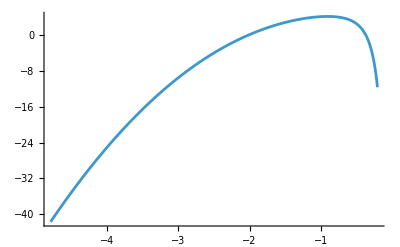

```mathematica
Plot[p[r],{r,xx0,xx1}]
```

```mathematica
r=r/.FindRoot[p[r],{r,-0.2}]
```

NIntegrate::inumr: 被積分関数((-6-30 r-20 r^2)/(5 r)+(14 r t)/5)/(r (((1-t) t)/(1+Power[«2»] t))^(1/4))は境界{{0,1}}の領域のすべてのサンプル点ついて，評価後に非数値になりました．

NIntegrate::inumr: 被積分関数(1/5 (-6-30 r-20 r^2)-(14 t)/5)/(((t (r^2+t))/(1-t))^(1/4))は境界{{0,1}}の領域のすべてのサンプル点ついて，評価後に非数値になりました．

NIntegrate::inumr: 被積分関数-(r (1/5 (-6-30 r-20 Power[«2»])-(14 t)/5) t)/(2 (1-t) ((t (r^2+t))/(1+Times[«2»]))^(5/4))+(-6-30 r-20 r^2)/(5 r ((t (r^2+t))/(1+Times[«2»]))^(1/4))は境界{{0,1}}の領域のすべてのサンプル点ついて，評価後に非数値になりました．

General::stop: この計算中に，NIntegrate::inumrのこれ以上の出力は表示されません．

-0.374404

## Region

```mathematica
ϵ=10.0^-7;
```

```mathematica
ν[z_]=StereographicProjection[g[z]];
```

```mathematica
q[z_]=ⅇ^z;
```

```mathematica
{xmin,xmax}={Re[Log[r]]-0.4,0};
{ymin,ymax}={0,π};
```

```mathematica
xspec=Sort[{Re[Log[r]],xmin,xmax}]
yspec=Sort[{ymin,π/2,ymax}]
```

{-1.38242,-0.982419,0}

{0,π/2,π}

```mathematica
nx1=3;
nx2=7;
ny=10;
```

```mathematica
Flatten[Table[FindRoot[Re[q[x+ⅈ 0]]==(j q[xspec[[1]]]+(nx1-j)q[xspec[[2]]])/nx1,{x,0.6}],{j,1,nx1}]]
```

{x→-1.09883,x→-1.23061,x→-1.38242}

```mathematica
prex01=Table[x/.%[[j]],{j,1,Length[%]}];
```

```mathematica
Flatten[Table[FindRoot[Re[q[x+ⅈ 0]]==(j q[xspec[[2]]]+(nx2-j)q[xspec[[3]]])/nx2,{x,0.6}],{j,1,nx2}]]
```

{x→-0.0936195,x→-0.196917,x→-0.312128,x→-0.442362,x→-0.592133,x→-0.768355,x→-0.982419}

```mathematica
prex02=Table[x/.%[[j]],{j,1,Length[%]}];
```

```mathematica
xr=Union[xspec,prex01,prex02];
yr=Union[NRange[yspec[[1]],yspec[[2]],ny],NRange[yspec[[2]],yspec[[3]],ny]]
```

{0.,0.174533,0.349066,0.523599,0.698132,0.872665,1.0472,1.22173,1.39626,1.5708,1.74533,1.91986,2.0944,2.26893,2.44346,2.61799,2.79253,2.96706,3.14159}

```mathematica
predomain=RectangularDomain[xr,yr];
```

```mathematica
Show[DomainToGraphics[predomain],AspectRatio->Automatic,Axes->True];
```

```mathematica
domain=MeshApply[q[#]&,predomain];
```

```mathematica
Show[DomainToGraphics[domain],AspectRatio->Automatic,Axes->True];
```

## Graphics of surface

```mathematica
dip[ins_][h_]:=$DisplayFunction[Insert[h,ins,{1,1}]];
```

```mathematica
Re[f[-1]]
```

{-2.34178,-4.23465,0.}

```mathematica
{x0,y0}={Re[f[1]][[1]],Re[f[r]][[2]]};
```

NIntegrate::ncvb: NIntegrateが{w} = {-0.37440437676965179132553250081753577624624148059914117207266401947+2.0185960050316521308896527171284586082848860431059596536748290391×10^-15 ⅈ}の近傍のwで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として4.23456-1.97063 ⅈと0.0000861872を得ました．

NIntegrate::ncvb: NIntegrateが{w} = {-0.37440437676965179132553250081753577624624148059914117207266401947+2.0185960050316521308896527171284586082848860431059596536748290391×10^-15 ⅈ}の近傍のwで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として-4.2345+4.69139 ⅈと0.0000867946を得ました．

```mathematica
gr1=MeshPlot3D[{Re[f[x+ⅈ y]]-{x0,y0,0},ν[x+ⅈ y]},{x,y},domain];
```

NIntegrate::ncvb: NIntegrateが{w} = {-0.37440437676965183820809640092202402411451598521155118942271224897+1.9392282577760244989192009654726613987610449264053277936905781792×10^-15 ⅈ}の近傍のwで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として4.23391-1.97017 ⅈと0.0000557118を得ました．

NIntegrate::ncvb: NIntegrateが{w} = {-0.37440437676965183820809640092202402411451598521155118942271224897+1.9392282577760244989192009654726613987610449264053277936905781792×10^-15 ⅈ}の近傍のwで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として-4.23495+4.69074 ⅈと0.0000563193を得ました．

NIntegrate::ncvb: NIntegrateが{w} = {-0.37440437676965283740881856355954709229610907957411124070812121522+1.9392282577760246221787174062520219667155246720682713190604693485×10^-15 ⅈ}の近傍のwで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として4.23295-1.97045 ⅈと0.000104469を得ました．

General::stop: この計算中に，NIntegrate::ncvbのこれ以上の出力は表示されません．

```mathematica
gr2=MeshJoin[gr1,MeshRotate[gr1,StraightLine[{0,0,0},{1,Tan[π/k],0}]]];
gr3=MeshJoin[gr2,MeshRotateX[gr2,π,0]];
gr4=MeshJoin[gr3,MeshRotateY[gr3,π,0]];
```

```mathematica
Show[Mesh3DToGraphics3D[gr4],Axes->True,Boxed->True,AxesLabel-> {"x","y","z"},DisplayFunction->dip[EdgeForm[Black]]];
```

```mathematica
gr5=Show[Mesh3DToGraphics3D[gr4],Boxed->False,DisplayFunction->dip[EdgeForm[Black]],ViewPoint->{1.671248170987841,-1.5331119987516972,2.5112740093931136},ViewVertical->{-0.029579348334531796,0.09971448094536682,0.9945763341452984},ImageSize->{ 600,600}];
```

```mathematica
g3d=Mesh3DToGraphics3D[gr4];

(*z座標の範囲を取得*)
pts=Cases[g3d,_Polygon,Infinity][[All,1]]//Flatten[#,1]&;
zvals=pts[[All,3]];
{zmin,zmax}={Min[zvals],Max[zvals]};

(*色付きGraphics3Dを作る*)
gr3d=Show[g3d/. Polygon[pts_]:>{ColorData["Rainbow"][(Mean[pts[[All,3]]]-zmin)/(zmax-zmin)],Polygon[pts]},Boxed->False,DisplayFunction->dip[EdgeForm[{}]],ImageSize->{600,600}];
Export["lm-hg-02-03-01.x3d",gr3d]
```

lm-hg-02-03-01.x3d